{{x→(-5-√(25-8 a))/(2 a)},{x→(-5+√(25-8 a))/(2 a)}}

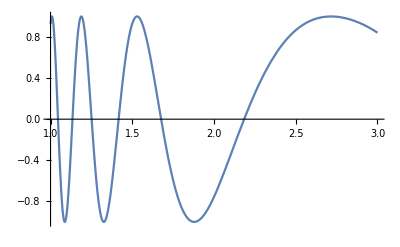

```mathematica
(* Příklad 6 *)
Solve[a*x^2+5x+2==0,x]
y=Sin[x^2] /. x ->(-5-√(25-8 a))/(2 a);
Plot[y,{a,1,3}]
```

```mathematica
(* Příklad 7 *)
z1=3+4ⅈ;
z2=4+5ⅈ;
Abs[z1+z2]
```

√130

```mathematica
(* Příklad 8 *)
urok = 0.1;
dni = 30;
du[castka_] := castka*urok/100/365;
duz[castka_] := Floor[du[castka], 0.01];
nextday[castka_] := Floor[(castka + duz[castka]), 0.01];
Nest[nextday,10000,30]
```

10000.6